```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
plotsDir= "../../plots/plots-104";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data1 = Import["../../runs/Trials/last.dat"];
data2 = Import["../../runs/Trials/last-shiva.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
matdata1 = cMat[data1];
matdata2 = cMat[data2];
```

```mathematica
eig1 = Flatten@(Eigenvalues/@matdata1[[All, 2]]);
eig2 = Flatten@(Eigenvalues/@matdata2[[All, 2]]);
```

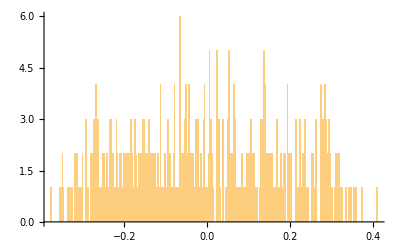

```mathematica
Histogram[eig1, 300]
```

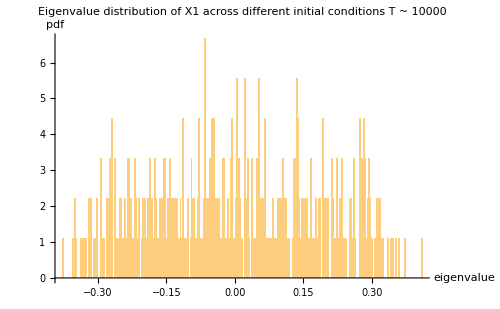

```mathematica
plt = Histogram[eig1, 300, PDF,
AxesLabel->{"eigenvalue", "pdf"},
PlotLabel->"Eigenvalue distribution of X1 across\n different initial conditions T ~ 10000",
ImageSize->500
]
```

```mathematica
Export[plotsDir<>"/spatial-dist-T10000.pdf", plt, ImageResolution->300]
```

../../plots/plots-104/spatial-dist-T10000.pdf